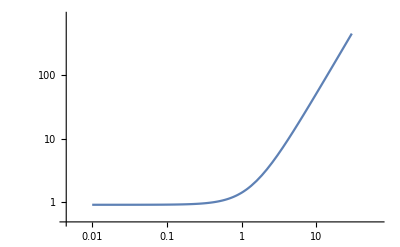

```mathematica
LogLogPlot[-Log[PDF[NormalDistribution[],x]],{x,0.01,30},PlotRange->All]
```

```mathematica
-Log[PDF[NormalDistribution[],x]]//FullSimplify
```

1/2 (-2 Log[ⅇ^(-x^2/2)]+Log[2 π])

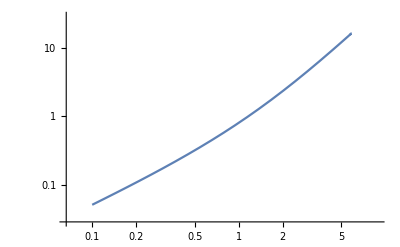

```mathematica
LogLogPlot[-Log10[1-Erf[x]],{x,0.1,1000},PlotRange->All]
```

```mathematica
Exp[D[x Log[-Log[1-Erf[x]]],x]]
```

-ⅇ^(-(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])) Log[1-Erf[x]]

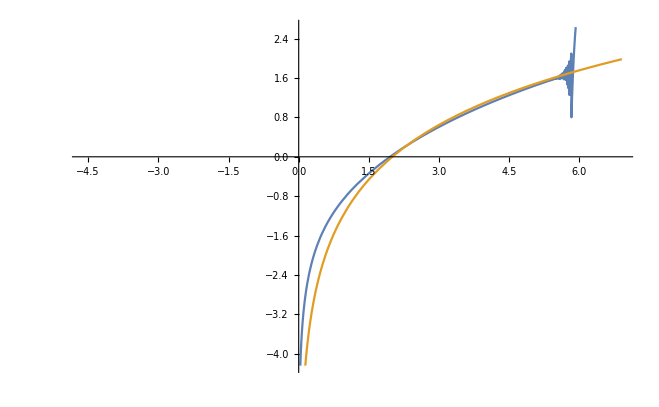

```mathematica
Plot[{(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])+Log[-Log[1-Erf[x]]],1.6Log[x/2]},{x,Log[.01],Log[1000]}]
```

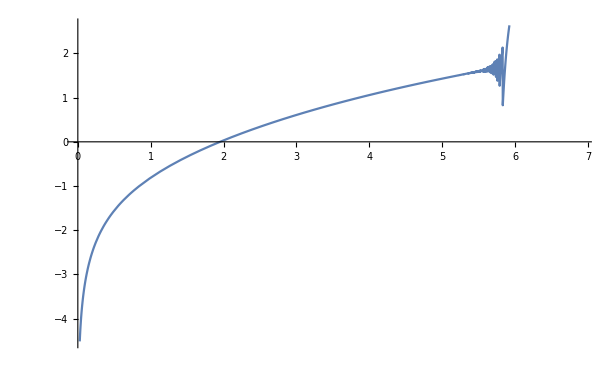

```mathematica
Plot[{(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])+Log[-Log[1-Erf[x]]]},{x,0,Log[1000]}]
```